## Introduced Intermediate Consumer (Ν): suboptimal defense toward Ν

Define Model

```mathematica
(* Modeling suboptimal defense -- Introduce ϕ the ratio of effeciency of introduced predator to recognized predator. As, ϕ goes to 1 defense against introduced pred is equally efficient. As it goes to zero defense effectiveness decreases. As efficiency shows up in the cost equations suboptimal response penalizes with NCEs as well  *)
```

```mathematica
Clear["Global`*"]
```

### Population Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional response of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resource *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fP (1-ϕ))- aPR P (1 - eP fP ));
dΝdt = Ν (bΝR aΝR (1- eΝ fP (1-ϕ)) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);
```

### Defense Effort and Fitness Dynamics

```mathematica
(*fitness is defined as the per capita growth rate of the resource*)
```

```mathematica
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fP (1-ϕ)) -  aPR P (1 - eP fP);
```

```mathematica
(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
```

eΝ v (aΝR (eΝ-1) fP Ν (ϕ-1)-aPR eP fP P+c0 r (eΝ+eP-1))

-eP v (-aΝR eΝ fP Ν (ϕ-1)+aPR (eP-1) fP P-c0 r (eΝ+eP-1))

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};
```

```mathematica
pars = {r-> 1,k-> 5, c0->0.25, fP->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ϕ->1};
parsCoex = {r-> 1,k-> 5, c0->0.25, fP->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
parsExc = {r-> 1,k-> 2.5, c0->0.4, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->1};
parsExcM = {r-> 1,k-> 2.5, c0->0.4, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->0.75};
parsExcL = {r-> 1,k-> 2.5, c0->0.4, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->0.49};

parsFacP = {r-> 1,k-> 0.7, c0->0.1, fP->0.8,  aPR-> 0.9, aPΝ -> .9, aΝR -> 0.8, bPΝ->0.5, bΝR->0.9, bPR->0.5, mP->0.5, mΝ->0.05, v-> 1, ϕ->1};
parsFacN = {r-> 1,k-> 0.28, c0->0.15, fP->0.8,  aPR-> 0.9, aPΝ -> 1.5, aΝR -> 0.8, bPΝ->0.5, bΝR->1, bPR->0.5, mP->0.3, mΝ->0.1, v-> 1, ϕ->1};
```

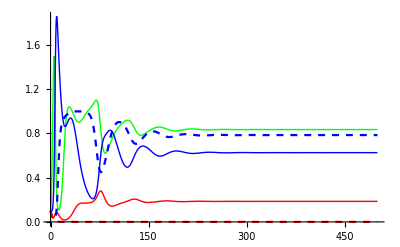

```mathematica
s=NDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsExc},{R,Ν, P, eΝ, eP},{t,0,500}];
Plot[Evaluate[{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[s]], {t,0,500}, PlotStyle-> cols]
```

### Manipulate across gradients ϕ

```mathematica
parsϕExc = Delete[parsExc, 14]
```

{r→1,k→2.5,c0→0.4,fP→0.8,aPR→0.9,aPΝ→0.4,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.1,v→1}

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[parsϕExc,{ϕ -> Φ}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{Φ,1,"ϕ"},0,1}];
```

#### Manipulate across gradient of k and others

```mathematica
parsGood =  {r->1,k->3,c0->0.1,fP->0.6,aPR->1,aPΝ->0.8,aΝR->0.8,bPΝ->0.5,bΝR->0.9,bPR->0.4,mP->0.55,mΝ->0.1,v->1, ϕ-> 1}
parsϕkaPΝc0 = Delete[parsGood, {{2}, {3},{6},{9},{11}, {14}}];
parsfacminus = Delete[parsFacN, {{2}, {3},{6},{9},{11}, {14}}];
```

{r→1,k→3,c0→0.1,fP→0.6,aPR→1,aPΝ→0.8,aΝR→0.8,bPΝ→0.5,bΝR→0.9,bPR→0.4,mP→0.55,mΝ→0.1,v→1,ϕ→1}

```mathematica
parsFacN
```

{r→1,k→0.28,c0→0.15,fP→0.8,aPR→0.9,aPΝ→1.5,aΝR→0.8,bPΝ→0.5,bΝR→1,bPR→0.5,mP→0.3,mΝ→0.1,v→1,ϕ→1}

```mathematica
{r->1,k->0.28,c0->0.15,fP->0.8,aPR->0.9,aPΝ->1.5,aΝR->0.8,bPΝ->0.5,bΝR->1,bPR->0.5,mP->0.3,mΝ->0.1,v->1,ϕ->1}
```

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[parsfacminus,{k -> κ, c0 -> χ, aPΝ -> α, ϕ -> Φ, bΝR-> β, mP-> μ}]},
{R,Ν, P, eΝ, eP},{t,0,500}]]],
{t,0,500},PlotRange->{0,All}, PlotStyle->cols],
{{κ,0.28,"k"},0,10}, {{χ,0.15,"c0"},0,1},{{α,1.5,"aPΝ"},0,2}, 
{{β,1,"bΝR"},0,1}, {{μ,.3,"mP"},0,1},{{Φ,1,"ϕ"},0,1}];
```

#### Comparison Plots

```mathematica
(*exclusion of P with increased novelty*)
```

```mathematica
parsExcPϕ = {r-> 1,k-> 2.5, c0->0.4, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1};
```

```mathematica
parsGoodϕ = Delete[parsGood, {14}]
```

{r→1,k→3,c0→0.1,fP→0.6,aPR→1,aPΝ→0.8,aΝR→0.8,bPΝ→0.5,bΝR→0.9,bPR→0.4,mP→0.55,mΝ→0.1,v→1}

```mathematica
finalϕ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsGoodϕ},{R,Ν, P, eΝ, eP},{t,0,1000}, {ϕ}];
```

```mathematica
Rfinalϕ = Plot[Evaluate[R[ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Green}, 
PlotRange->{{0,1},{0,2}}];
Νfinalϕ = Plot[Evaluate[Ν[ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Blue},  
PlotRange->{{0,1},{0,2}}];
Pfinalϕ = Plot[Evaluate[P[ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle->  {Thickness[0.015], Red},  
PlotRange->{{0,1},{0,2}}];
eΝfinalϕ = Plot[Evaluate[eΝ[ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015],Blue, Dashed}, 
PlotRange->{{0,1},{0,2}}];
ePfinalϕ = Plot[Evaluate[eP[ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Red, Dashed}, 
PlotRange->{{0,1},{0,2}}];
```

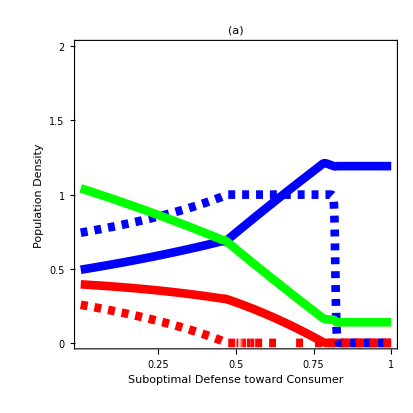

```mathematica
Fig7a = Show[Νfinalϕ,Pfinalϕ,eΝfinalϕ, ePfinalϕ,Rfinalϕ, Frame-> True, FrameLabel->{"Suboptimal Defense toward Consumer","Population Density", "","Defense Effort"}, ImageSize -> 414,Spacings-> 30,
PlotLabel -> Style["(a)                                                                                       ", FontSize->14,  Bold],
AspectRatio -> 1/1, LabelStyle-> {Black, Larger}, FrameTicks->{{{0,0.5,1, 1.5, 2},
{0.5,1, 1.5, 2}},{{1, 0.75, 0.5, 0.25}, {None}}}]
```

```mathematica
Export["C:\\Users\\ingemank\\Desktop\\MoNSTR\\Dissertation Figures\\MoNSTR_Fig8_Full.tif",Fig8,"TIFF", ImageResolution-> 600]
```

```mathematica
(*coexistence via increased novelty*)
```

```mathematica
parsFacNϕ = Delete[parsFacN, 14]
```

{r→1,k→0.28,c0→0.15,fP→0.8,aPR→0.9,aPΝ→1.5,aΝR→0.8,bPΝ→0.5,bΝR→1,bPR→0.5,mP→0.3,mΝ→0.1,v→1}

```mathematica
finalFacϕ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsFacNϕ},{R,Ν, P, eΝ, eP},{t,0,500}, {ϕ}];
```

```mathematica
RfinalϕFac = Plot[Evaluate[R[ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Green}, 
PlotRange->{{0,0.28},{0,0.6}}];
ΝfinalϕFac = Plot[Evaluate[Ν[ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Blue},  
PlotRange->{{0,0.28},{0,0.6}}];
PfinalϕFac = Plot[Evaluate[P[ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle->  {Thickness[0.015], Red},  
PlotRange->{{0,0.28},{0,0.6}}];
eΝfinalϕFac = Plot[Evaluate[eΝ[ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015],Blue, Dashed}, 
PlotRange->{{0,0.28},{0,0.6}}];
ePfinalϕFac = Plot[Evaluate[eP[ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Red, Dashed}, 
PlotRange->{{0,0.28},{0,0.6}}];
```

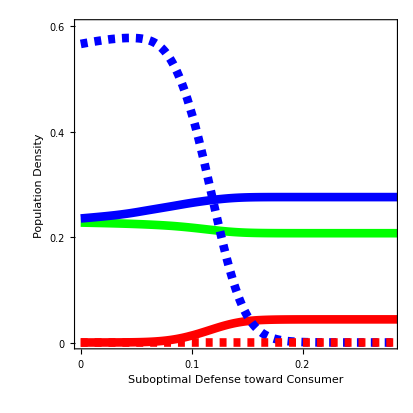

```mathematica
Fig8=Show[RfinalϕFac,ΝfinalϕFac,PfinalϕFac,eΝfinalϕFac, ePfinalϕFac, 
Frame-> True, FrameLabel->{"Suboptimal Defense toward Consumer","Population Density", "","Defense Effort"}, ImageSize -> 414,Spacings-> 30, 
AspectRatio -> 1/1, LabelStyle-> {Black, Larger}, FrameTicks->{{{0,0.2,0.4, 0.6},
{0,0.2,0.4, 0.6}},{{0, 0.1, 0.2}, {None}}}]
```

```mathematica
Export["C:\\Users\\ingemank\\Desktop\\MoNSTR\\Dissertation Figures\\MoNSTR_Fig8_Full.tif",Fig8,"TIFF", ImageResolution-> 600]
```

C:\Users\ingemank\Desktop\MoNSTR\Dissertation Figures\MoNSTR_Fig8_Full.tif

```mathematica
Export["MoNSTR_Fig8_Full.pdf",Fig8]
```

MoNSTR_Fig8_Full.pdf

### PLot final densities across a range of c0

```mathematica
c0parsϕH = {r-> 1,k-> 2.5, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->1};
c0parsϕM =  {r-> 1,k-> 2.5, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->.75};
c0parsϕL =  {r-> 1,k-> 2.5, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->.5};
```

```mathematica
c0finalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕH},{R,Ν, P, eΝ, eP},{t,0,1000}, {c0}];
c0finalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕM },{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
c0finalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕL},{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
```

```mathematica
c0finalRH = Plot[Evaluate[R[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝH = Plot[Evaluate[Ν[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPH = Plot[Evaluate[P[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝH = Plot[Evaluate[eΝ[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePH = Plot[Evaluate[eP[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

```mathematica
c0finalRM = Plot[Evaluate[R[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝM = Plot[Evaluate[Ν[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPM = Plot[Evaluate[P[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝM = Plot[Evaluate[eΝ[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePM = Plot[Evaluate[eP[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

```mathematica
c0finalRL = Plot[Evaluate[R[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝL  = Plot[Evaluate[Ν[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPL  = Plot[Evaluate[P[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝL = Plot[Evaluate[eΝ[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePL = Plot[Evaluate[eP[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

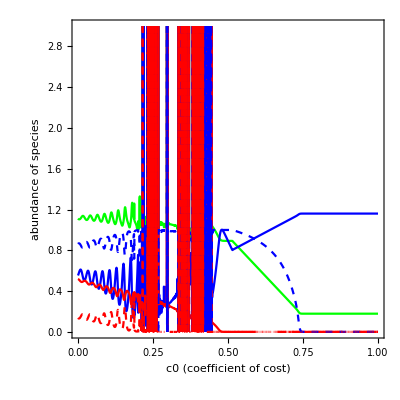

```mathematica
Show[c0finalRH,c0finalΝH,c0finalPH,c0finaleΝH, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

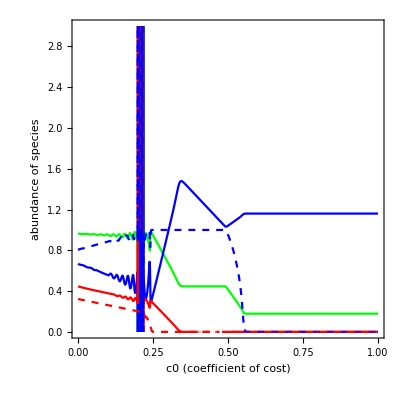

```mathematica
Show[c0finalRM,c0finalΝM,c0finalPM,c0finaleΝM, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

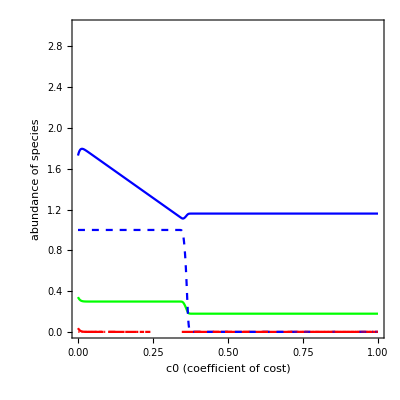

```mathematica
Show[c0finalRL,c0finalΝL,c0finalPL,c0finaleΝL, c0finalePL, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

Determine equilibria

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
equil//TableForm
```

R→0 | Ν→0 | P→0 | eP→1-eΝ | 
R→-(c0-1) k r | Ν→0 | P→0 | eP→1-eΝ | 
R→mP/(aPR bPR) | Ν→0 | P→(aPR r-mP/(bPR k))/aPR^2 | eΝ→0 | eP→0
R→mP/(aPR bPR) | Ν→0 | P→-(aPR bPR (c0-1) k r+mP)/(aPR^2 bPR k) | eΝ→1 | eP→0
R→mP/(aPR bPR-aPR bPR fP) | Ν→0 | P→(aPR bPR (c0-1) (fP-1) k r-mP)/(aPR^2 bPR (fP-1)^2 k) | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→mP/(aPR bPR fP k r-aPR bPR c0 fP k r)-1/fP+1 | eP→(1-mP/(aPR bPR k r-aPR bPR c0 k r))/fP
R→(k r (fP-c0))/fP | Ν→0 | P→(c0 r)/(aPR fP) | eΝ→0 | eP→mP/(aPR bPR c0 k r-aPR bPR fP k r)+1/fP
R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
R→-(k (aΝR mP+aPΝ bPΝ (c0-1) r+aPR bPΝ (fP-1) mΝ))/(aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR k r (c0 (-fP)+c0+fP-1)+mP)-aPR (fP-1) k (aΝR bΝR mP+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPΝ bΝR bPΝ (c0-1) r+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | eΝ→0 | eP→1
R→(aPΝ c0 r+aPR fP mΝ)/(aΝR aPR bΝR fP) | Ν→(-aPΝ c0 r+aΝR aPR bΝR k r (fP-c0)-aPR fP mΝ)/(aΝR^2 aPR bΝR fP k) | P→(c0 r)/(aPR fP) | eΝ→0 | eP→(aPΝ r (aΝR aPR k (bΝR bPΝ (fP-c0)+bPR c0)-aPΝ bPΝ c0)+aPR fP (aΝR k (aPR bPR mΝ-aΝR bΝR mP)-aPΝ bPΝ mΝ))/(aΝR aPR bPR fP k (aPΝ c0 r+aPR fP mΝ))
R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR) | Ν→-(aΝR bΝR (c0-1) k r+mΝ)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR) | Ν→(aΝR r-mΝ/(bΝR k))/aΝR^2 | P→0 | eΝ→0 | eP→0
R→(k (aΝR mP (fP ϕ-1)+bPΝ (aPR mΝ-aPΝ (c0-1) r)))/(aPΝ bPΝ+aΝR aPR k (fP ϕ-1) (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR (c0-1) k r+mP)-aPR k (aΝR bΝR mP (fP ϕ-1)+aPR bPR mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR k (fP ϕ-1) (bPR-bΝR bPΝ))) | P→-(aPΝ bPΝ mΝ+aΝR k (fP ϕ-1) (aΝR bΝR mP (fP ϕ-1)-aPΝ bΝR bPΝ (c0-1) r+aPR bPR mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR k (fP ϕ-1) (bPR-bΝR bPΝ))) | eΝ→1 | eP→0
R→mΝ/(aΝR bΝR-aΝR bΝR fP ϕ) | Ν→(aΝR bΝR (c0-1) k r (fP ϕ-1)-mΝ)/(aΝR^2 bΝR k (fP ϕ-1)^2) | P→0 | eΝ→1 | eP→0
R→-(k r (c0 ϕ+c0-fP ϕ))/(fP ϕ) | Ν→(c0 r)/(aΝR fP ϕ) | P→(c0 r)/(aPR fP) | eΝ→-(aPΝ c0 r ϕ+aPR (aΝR bΝR k r (c0 ϕ+c0-fP ϕ)+fP mΝ ϕ))/(aΝR aPR bΝR fP k r ϕ (fP ϕ-c0 (ϕ+1))) | eP→(aPΝ bPΝ c0 r-aΝR (aPR bPR k r (c0 ϕ+c0-fP ϕ)+fP mP ϕ))/(aΝR aPR bPR fP k r (fP ϕ-c0 (ϕ+1)))
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→(aΝR bΝR c0 k r-aΝR bΝR k r+mΝ)/(aΝR bΝR c0 fP k r ϕ-aΝR bΝR fP k r ϕ) | eP→(aΝR bΝR (c0-1) k r (fP ϕ-1)-mΝ)/(aΝR bΝR (c0-1) fP k r ϕ)
R→(k (ϕ (aΝR bΝR mP (-fP ϕ+ϕ+1)-aPΝ (c0-1) r (bPR-bΝR bPΝ))+aPR bPR mΝ (-fP ϕ+ϕ+1)))/(aPΝ ϕ (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (-fP ϕ+ϕ+1)^2) | Ν→-(aΝR bΝR mP ϕ+aPR bPR (mΝ-aΝR bΝR (c0-1) k r ((fP-1) ϕ-1)))/(aΝR (aPΝ ϕ (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (-fP ϕ+ϕ+1)^2)) | P→(ϕ (aPR bPR (aΝR bΝR (c0-1) k r ((fP-1) ϕ-1)-mΝ)-aΝR bΝR mP ϕ))/(aPR (aPΝ ϕ (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (-fP ϕ+ϕ+1)^2)) | eΝ→(-aΝR aPΝ mP ϕ+aΝR aPR^2 bPR (fP-1) k mΝ ((fP-1) ϕ-1)+aPR (aΝR k (aΝR bΝR mP ((fP-1) ϕ-1)+aPΝ (c0-1) r (bPR (fP-1) ϕ-bΝR bPΝ))-aPΝ bPΝ mΝ))/(aΝR aPR fP k (ϕ (aΝR bΝR mP ((fP-1) ϕ-1)+aPΝ (c0-1) r (bPR-bΝR bPΝ))+aPR bPR mΝ ((fP-1) ϕ-1))) | eP→(aΝR aPΝ mP ϕ+aΝR aPR^2 bPR k mΝ ((fP-1) ϕ-1)+aPR (aΝR k (aΝR bΝR mP ((fP-1) ϕ-1) (fP ϕ-1)+aPΝ (c0-1) r (-bΝR bPΝ fP ϕ+bΝR bPΝ+bPR ϕ))+aPΝ bPΝ mΝ))/(aΝR aPR fP k (ϕ (aΝR bΝR mP ((fP-1) ϕ-1)+aPΝ (c0-1) r (bPR-bΝR bPΝ))+aPR bPR mΝ ((fP-1) ϕ-1)))
R→(aΝR fP mP ϕ-aPΝ bPΝ c0 r)/(aΝR aPR bPR fP ϕ) | Ν→(c0 r)/(aΝR fP ϕ) | P→(aPΝ bPΝ c0 r-aΝR (aPR bPR k r (c0-fP ϕ)+fP mP ϕ))/(aΝR aPR^2 bPR fP k ϕ) | eΝ→((aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))/(aΝR aPR fP k ϕ)+(bPR (-aΝR mP+aPΝ bPΝ r+aPR bPΝ mΝ))/(aPΝ bPΝ c0 r-aΝR fP mP ϕ))/(bΝR bPΝ) | eP→0
R→k r (1-c0/(fP ϕ)) | Ν→(c0 r)/(aΝR fP ϕ) | P→0 | eΝ→mΝ/(aΝR bΝR c0 k r-aΝR bΝR fP k r ϕ)+1/(fP ϕ) | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
R→(k (-aΝR mP+aPΝ bPΝ r+aPR bPΝ mΝ))/(aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | P→(aΝR k (-aΝR bΝR mP+aPΝ bΝR bPΝ r+aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | eΝ→0 | eP→0
R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→1 | eP→0
R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

Determine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(aΝR eΝ fP Ν ϕ-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aΝR R (eΝ fP ϕ-1) | R (aΝR fP Ν ϕ-c0 r) | aPR R (eP fP-1) | R (aPR fP P-c0 r)
aΝR bΝR Ν (1-eΝ fP ϕ) | aΝR bΝR R (1-eΝ fP ϕ)-aPΝ P-mΝ | -aΝR bΝR fP Ν R ϕ | -aPΝ Ν | 0
0 | -aΝR (eΝ-1) eΝ fP v ϕ | v (aΝR (1-2 eΝ) fP Ν ϕ-aPR eP fP P+c0 r (2 eΝ+eP-1)) | -aPR eΝ eP fP v | eΝ v (c0 r-aPR fP P)
aPR bPR P (1-eP fP) | aPΝ bPΝ P | 0 | aPΝ bPΝ Ν+aPR bPR R (1-eP fP)-mP | -aPR bPR fP P R
0 | -aΝR eΝ eP fP v ϕ | eP v (c0 r-aΝR fP Ν ϕ) | -aPR (eP-1) eP fP v | v (-aΝR eΝ fP Ν ϕ+aPR (1-2 eP) fP P+c0 r (eΝ+2 eP-1)))

(aΝR eΝ fP Ν ϕ-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aΝR R (eΝ fP ϕ-1) | R (aΝR fP Ν ϕ-c0 r)
aΝR bΝR Ν (1-eΝ fP ϕ) | aΝR bΝR R (1-eΝ fP ϕ)-aPΝ P-mΝ | -aΝR bΝR fP Ν R ϕ
0 | -aΝR (eΝ-1) eΝ fP v ϕ | v (aΝR (1-2 eΝ) fP Ν ϕ-aPR eP fP P+c0 r (2 eΝ+eP-1)))

(aΝR eΝ fP Ν ϕ-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aPR R (eP fP-1) | R (aPR fP P-c0 r)
aPR bPR P (1-eP fP) | aPΝ bPΝ Ν+aPR bPR R (1-eP fP)-mP | -aPR bPR fP P R
0 | -aPR (eP-1) eP fP v | v (-aΝR eΝ fP Ν ϕ+aPR (1-2 eP) fP P+c0 r (eΝ+2 eP-1)))

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subpars=Delete[parsExc,2];
subparsM=Delete[parsExcM,2];
subparsL=Delete[parsExcL,2];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq14RΝ=JRΝ/.equil[[14,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq16RΝ=JRΝ/.equil[[16,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq3RP=JRP/.equil[[3,All]]//FullSimplify;
Jeq7RP=JRP/.equil[[7,All]]//FullSimplify;
Jeq5RP=JRP/.equil[[5,All]]//FullSimplify;
```

```mathematica
AllFeas3[k_]=AllTrue[Re[equil[[3,All,2]]/.subpars],#≥0&];
AllFeas5[k_]=AllTrue[Re[equil[[5,All,2]]/.subpars],#≥0&];
AllFeas7[k_]=AllTrue[Re[equil[[7,All,2]]/.subpars],#≥0&];
AllFeas14[k_]=AllTrue[Re[equil[[14,All,2]]/.subpars],#≥0&];
AllFeas21[k_]=AllTrue[Re[equil[[21,All,2]]/.subpars],#≥0&];
AllFeas16[k_]=AllTrue[Re[equil[[16,All,2]]/.subpars],#≥0&];

AllFeas3M[k_]=AllTrue[Re[equil[[3,All,2]]/.subparsM],#≥0&];
AllFeas5M[k_]=AllTrue[Re[equil[[5,All,2]]/.subparsM],#≥0&];
AllFeas7M[k_]=AllTrue[Re[equil[[7,All,2]]/.subparsM],#≥0&];
AllFeas14M[k_]=AllTrue[Re[equil[[14,All,2]]/.subparsM],#≥0&];
AllFeas21M[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];
AllFeas16M[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];

AllFeas3L[k_]=AllTrue[Re[equil[[3,All,2]]/.subparsL],#≥0&];
AllFeas5L[k_]=AllTrue[Re[equil[[5,All,2]]/.subparsL],#≥0&];
AllFeas7L[k_]=AllTrue[Re[equil[[7,All,2]]/.subparsL],#≥0&];
AllFeas14L[k_]=AllTrue[Re[equil[[14,All,2]]/.subparsL],#≥0&];
AllFeas21L[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];
AllFeas16L[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];
```

```mathematica
pReEig14RΝ[k_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subpars]]]]; 
pReEig21RΝ[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subpars]]]];
pReEig16RΝ[k_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subpars]]]];

pReEig14RΝM[k_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsM]]]]; 
pReEig21RΝM[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig16RΝM[k_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsM]]]];

pReEig14RΝL[k_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsL]]]]; 
pReEig21RΝL[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig16RΝL[k_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig3RP[k_]=Max[Re[Eigenvalues[N[Jeq3RP/.subpars]]]];
pReEig7RP[k_]=Max[Re[Eigenvalues[N[Jeq7RP/.subpars]]]];
pReEig5RP[k_]=Max[Re[Eigenvalues[N[Jeq5RP/.subpars]]]];

pReEig3RPM[k_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsM]]]];
pReEig7RPM[k_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsM]]]];
pReEig5RPM[k_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsM]]]];

pReEig3RPL[k_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsL]]]];
pReEig7RPL[k_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsL]]]];
pReEig5RPL[k_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsL]]]];
```

Produce Plots

```mathematica
kaPΝparsH = Delete[parsExc, {{2},{6}}];
kaPΝparsM = Delete[parsExcM, {{2},{6}}];
kaPΝparsL = Delete[parsExcL, {{2},{6}}];
```

```mathematica
RstarRN14 = equil[[14,1,2]];
NstarRN14= equil[[14,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN16 = equil[[16,1,2]];
NstarRN16= equil[[16,2,2]];
```

```mathematica
PinvRN14 = bPR aPR (1 -0*fP)RstarRN14  + aPN bPΝ NstarRN14 - mP;
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP;
PinvRN16 = bPR aPR (1 -0*fP)RstarRN16  + aPN bPΝ NstarRN16 - mP;
```

### High Efficiency

```mathematica
plotPinvRN14 = FullSimplify[Solve[PinvRN14==0,aPN]][[1,1,2]];
PinvRN14kaPN = plotPinvRN14/.kaPΝparsH;
PlotRN14 = Plot[PinvRN14kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig14RΝ[x]<0&&AllFeas14[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.kaPΝparsH;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];

plotPinvRN16 = FullSimplify[Solve[PinvRN16==0,aPN]][[1,1,2]];
PinvRN16kaPN = plotPinvRN16/.kaPΝparsH;
PlotRN16 = Plot[PinvRN16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig16RΝ[x]<0&&AllFeas16[x]]];
```

```mathematica
Rstar3 = equil[[3,1,2]];
Pstar3= equil[[3,3,2]];
Rstar7 = equil[[7,1,2]];
Pstar7= equil[[7,3,2]];
Rstar5 = equil[[5,1,2]];
Pstar5= equil[[5,3,2]];
```

```mathematica
Νinv3 = bΝR aΝR (1 -0*fΝ)Rstar3  - aPΝ Pstar3 - mΝ;
Νinv7 = bΝR aΝR (1 -0*fΝ)Rstar7  - aPΝ Pstar7 - mΝ;
Νinv5= bΝR aΝR (1 -0*fΝ)Rstar5 - aPΝ Pstar5 - mΝ;
```

```mathematica
plotΝinv3= FullSimplify[Solve[Νinv3==0,aPΝ]][[1,1,2]];
Νinv3kaPN = plotΝinv3/.kaPΝparsH;
PlotRP3 = Plot[Νinv3kaPN,{k, 1.1112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle->White, AspectRatio -> 1/1, 
RegionFunction->Function[{x},pReEig3RP[x]<0&&AllFeas3[x]]];

plotΝinv7= FullSimplify[Solve[Νinv7==0,aPΝ]][[1,1,2]];
Νinv7kaPN = plotΝinv7/.kaPΝparsH;
PlotRP7 = Plot[Νinv7kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig7RP[x]<0&&AllFeas7[x]]];

plotΝinv5= FullSimplify[Solve[Νinv5==0,aPΝ]][[1,1,2]];
Νinv5kaPN = plotΝinv5/.kaPΝparsH;
PlotRP5 = Plot[Νinv5kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,LabelStyle-> {Larger, Black},
RegionFunction->Function[{x},pReEig5RP[x]<0&&AllFeas5[x]]];
```

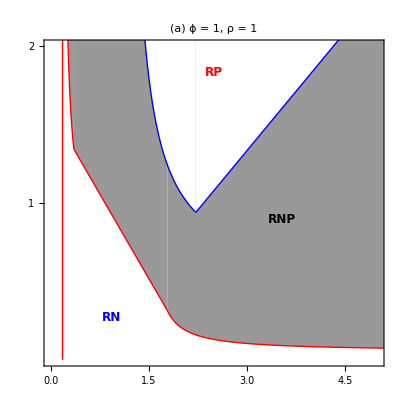

```mathematica
Fig5a =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.45}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.2,0.15}]]}],
PlotLabel -> Style["(a)    ϕ = 1, ρ = 1", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,2}},FrameTicks->{{{1, 2},{None}},{{None}, {None}}}]
```

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN14kaPN = plotPinvRN14/.kaPΝparsM;
PlotRN14 = Plot[PinvRN14kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig14RΝM[x]<0&&AllFeas14M[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsM;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

PinvRN16kaPN = plotPinvRN16/.kaPΝparsM;
PlotRN16 = Plot[PinvRN16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig16RΝM[x]<0&&AllFeas16M[x]]];

Νinv3kaPN = plotΝinv3/.kaPΝparsM;
PlotRP3 = Plot[Νinv3kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig3RPM[x]< 0&&AllFeas3M[x]]];

Νinv7kaPN = plotΝinv7/.kaPΝparsM;
PlotRP7 = Plot[Νinv7kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig7RPM[x]<0&&AllFeas7M[x]]];

Νinv5kaPN = plotΝinv5/.kaPΝparsM;
PlotRP5 = Plot[Νinv5kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig5RPM[x]<0&&AllFeas5M[x]]];
```

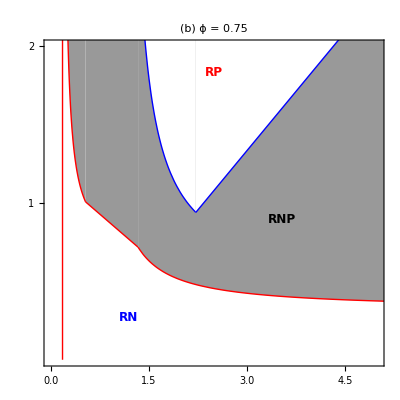

```mathematica
Fig5b =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.45}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.25,0.15}]]}],
PlotLabel -> Style["(b)    ϕ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,2}},FrameTicks->{{{1, 2},{None}},{{None}, {None}}}]
```

#### Low relative efficiency (ϕ = 0.5)

```mathematica
PinvRN14kaPN = plotPinvRN14/.kaPΝparsL;
PlotRN14 = Plot[PinvRN14kaPN,{k, 0,1.112}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig14RΝL[x]<0&&AllFeas14L[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsL;
PlotRN21 = Plot[PinvRN21kaPN,{k, 1.112,1.85}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6]];

PinvRN16kaPN = plotPinvRN16/.kaPΝparsL;
PlotRN16 = Plot[PinvRN16kaPN,{k, 1.85,6}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6]];

Νinv3kaPN = plotΝinv3/.kaPΝparsL;
PlotRP3 = Plot[Νinv3kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle->White,AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
RegionFunction->Function[{x},pReEig3RPL[x]< 0&&AllFeas3L[x]]];

Νinv7kaPN = plotΝinv7/.kaPΝparsL;
PlotRP7 = Plot[Νinv7kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig7RPL[x]<0&&AllFeas7L[x]]];

Νinv5kaPN = plotΝinv5/.kaPΝparsL;
PlotRP5 = Plot[Νinv5kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig5RPL[x]<0&&AllFeas5L[x]]];
```

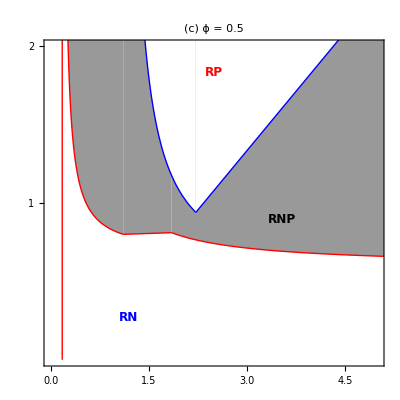

```mathematica
Fig5c= Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.45}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.25,0.15}]]}],
PlotLabel -> Style["(c)    ϕ = 0.5", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,2}},FrameTicks->{{{1, 2},{None}},{{None}, {None}}}]
```

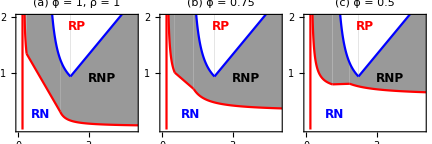
-Graphics-productivity (k)IGP strength

```mathematica
Figure5abc = Panel[GraphicsRow[{Fig5a,Fig5b,Fig5c}, ImageSize-> 432, Spacings->0], {"productivity (k)",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White]
```

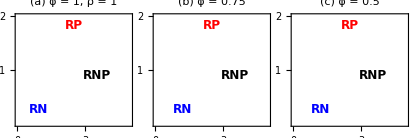
-Graphics-productivity (k)IGP strength

```mathematica
Figure5abcDIS = Panel[GraphicsRow[{Fig5a,Fig5b,Fig5c}, ImageSize-> 414, Spacings->0], {"productivity (k)",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White]
```

## Plot cost against IGP strength

### Functions for working with equilibrium values across a gradient of productivity (c0)

```mathematica
parsGood =  {r->1,k->3,c0->0.1,fP->0.6,aPR->1,aPΝ->0.8,aΝR->0.8,bPΝ->0.5,bΝR->0.9,bPR->0.4,mP->0.55,mΝ->0.1,v->1, ϕ-> 1};
parsGoodM =  {r->1,k->3,c0->0.1,fP->0.6,aPR->1,aPΝ->0.8,aΝR->0.8,bPΝ->0.5,bΝR->0.9,bPR->0.4,mP->0.55,mΝ->0.1,v->1, ϕ-> 0.75};
parsGoodL =  {r->1,k->3,c0->0.1,fP->0.6,aPR->1,aPΝ->0.8,aΝR->0.8,bPΝ->0.5,bΝR->0.9,bPR->0.4,mP->0.55,mΝ->0.1,v->1, ϕ-> 0.5};
```

```mathematica
subpars=Delete[parsExc,3];
subparsM=Delete[parsExcM,3];
subparsL=Delete[parsExcL,3];
```

```mathematica
AllFeas3[c0_]=AllTrue[Re[equil[[3,All,2]]/.subpars],#≥0&];
AllFeas5[c0_]=AllTrue[Re[equil[[5,All,2]]/.subpars],#≥0&];
AllFeas7[c0_]=AllTrue[Re[equil[[7,All,2]]/.subpars],#≥0&];
AllFeas14[c0_]=AllTrue[Re[equil[[14,All,2]]/.subpars],#≥0&];
AllFeas21[c0_]=AllTrue[Re[equil[[21,All,2]]/.subpars],#≥0&];
AllFeas16[c0_]=AllTrue[Re[equil[[16,All,2]]/.subpars],#≥0&];

AllFeas3M[c0_]=AllTrue[Re[equil[[3,All,2]]/.subparsM],#≥0&];
AllFeas5M[c0_]=AllTrue[Re[equil[[5,All,2]]/.subparsM],#≥0&];
AllFeas7M[c0_]=AllTrue[Re[equil[[7,All,2]]/.subparsM],#≥0&];
AllFeas14M[c0_]=AllTrue[Re[equil[[14,All,2]]/.subparsM],#≥0&];
AllFeas21M[c0_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];
AllFeas16M[c0_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];

AllFeas3L[c0_]=AllTrue[Re[equil[[3,All,2]]/.subparsL],#≥0&];
AllFeas5L[c0_]=AllTrue[Re[equil[[5,All,2]]/.subparsL],#≥0&];
AllFeas7L[c0_]=AllTrue[Re[equil[[7,All,2]]/.subparsL],#≥0&];
AllFeas14L[c0_]=AllTrue[Re[equil[[14,All,2]]/.subparsL],#≥0&];
AllFeas21L[c0_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];
AllFeas16L[c0_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];

pReEig14RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subpars]]]]; 
pReEig21RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subpars]]]];
pReEig16RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subpars]]]];

pReEig14RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsM]]]]; 
pReEig21RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig16RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsM]]]];

pReEig14RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsL]]]]; 
pReEig21RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig16RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsL]]]];
pReEig3RP[c0_]=Max[Re[Eigenvalues[N[Jeq3RP/.subpars]]]];
pReEig7RP[c0_]=Max[Re[Eigenvalues[N[Jeq7RP/.subpars]]]];
pReEig5RP[c0_]=Max[Re[Eigenvalues[N[Jeq5RP/.subpars]]]];

pReEig3RPM[c0_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsM]]]];
pReEig7RPM[c0_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsM]]]];
pReEig5RPM[c0_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsM]]]];

pReEig3RPL[c0_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsL]]]];
pReEig7RPL[c0_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsL]]]];
pReEig5RPL[c0_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsL]]]];
```

### Invasibility Plot (c0 and aPN)

#### P invades RN

```mathematica
c0aPΝparsH = Delete[parsExc, {{3},{6}}];
c0aPΝparsM = Delete[parsExcM, {{3},{6}}];
c0aPΝparsL = Delete[parsExcL, {{3},{6}}];
```

#### High relative efficiency (ϕ = 1)

```mathematica
PinvRN14c0aPN = plotPinvRN14/.c0aPΝparsH;
PlotRN14 = Plot[PinvRN14c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig14RΝ[x]<0&&AllFeas14[x]]];

PinvRN21c0aPN = plotPinvRN21/.c0aPΝparsH;
PlotRN21 = Plot[PinvRN21c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];

PinvRN16c0aPN = plotPinvRN16/.c0aPΝparsH;
PlotRN16 = Plot[PinvRN16c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig16RΝ[x]<0&&AllFeas16[x]]];

Νinv3c0aPN= plotΝinv3/.c0aPΝparsH;
PlotRP3 = Plot[Νinv3c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig3RP[x]<0&&AllFeas3[x]]];

Νinv7c0aPN= plotΝinv7/.c0aPΝparsH;
PlotRP7 = Plot[Νinv7c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig7RP[x]<0&&AllFeas7[x]]];

Νinv5c0aPN = plotΝinv5/.c0aPΝparsH;
PlotRP5 = Plot[Νinv5c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig5RP[x]<0&&AllFeas5[x]]];
```

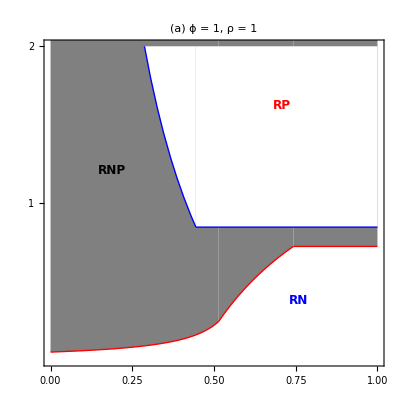

```mathematica
Fig6a =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.7,0.8}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.75,0.2}]]}],
PlotLabel -> Style["(a)    ϕ = 1, ρ = 1", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{1, 2},{None}},{{None}, {None}}}]
```

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN14c0aPN = plotPinvRN14/.c0aPΝparsM;
PlotRN14 = Plot[PinvRN14c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig14RΝM[x]<0&&AllFeas14M[x]]];

PinvRN21c0aPN = plotPinvRN21/.c0aPΝparsM;
PlotRN21 = Plot[PinvRN21c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

PinvRN16c0aPN = plotPinvRN16/.c0aPΝparsM;
PlotRN16 = Plot[PinvRN16c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig16RΝM[x]<0&&AllFeas16M[x]]];

Νinv3c0aPN= plotΝinv3/.c0aPΝparsM;
PlotRP3 = Plot[Νinv3c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig3RPM[x]<0&&AllFeas3M[x]]];

Νinv7c0aPN= plotΝinv7/.c0aPΝparsM;
PlotRP7 = Plot[Νinv7c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig7RPM[x]<0&&AllFeas7M[x]]];

Νinv5c0aPN = plotΝinv5/.c0aPΝparsM;
PlotRP5 = Plot[Νinv5c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig5RPM[x]<0&&AllFeas5M[x]]];
```

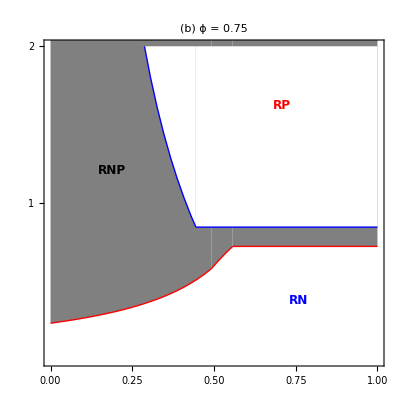

```mathematica
Fig6b =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.7,0.8}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.75,0.2}]]}],
PlotLabel -> Style["(b)    ϕ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{1, 2},{None}},{{None}, {None}}}]
```

#### Low relative efficiency (ϕ = 0.5)

```mathematica
PinvRN14c0aPN = plotPinvRN14/.c0aPΝparsL;
PlotRN14 = Plot[PinvRN14c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig14RΝL[x]<0&&AllFeas14L[x]]];

PinvRN21c0aPN = plotPinvRN21/.c0aPΝparsL;
PlotRN21 = Plot[PinvRN21c0aPN,{c0, 0.34,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝL[x]<0&&AllFeas21L[x]]];

PinvRN16c0aPN = plotPinvRN16/.c0aPΝparsL;
PlotRN16 = Plot[PinvRN16c0aPN,{c0, 0,0.35}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig16RΝL[x]<0&&AllFeas16L[x]]];

Νinv3c0aPN= plotΝinv3/.c0aPΝparsL;
PlotRP3 = Plot[Νinv3c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig3RPL[x]<0&&AllFeas3L[x]]];

Νinv7c0aPN= plotΝinv7/.c0aPΝparsL;
PlotRP7 = Plot[Νinv7c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig7RPL[x]<0&&AllFeas7L[x]]];

Νinv5c0aPN = plotΝinv5/.c0aPΝparsL;
PlotRP5 = Plot[Νinv5c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig5RPL[x]<0&&AllFeas5L[x]]];
```

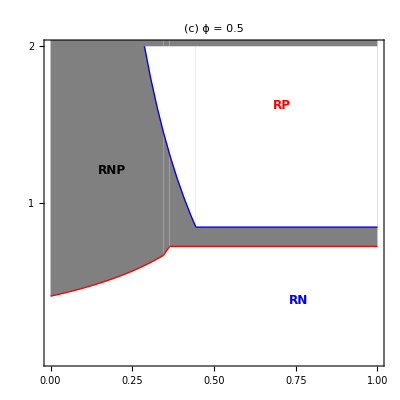

```mathematica
Fig6c =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.7,0.8}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.75,0.2}]]}],
PlotLabel -> Style["(c)    ϕ = 0.5", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{1, 2},{None}},{{None}, {None}}}]
```

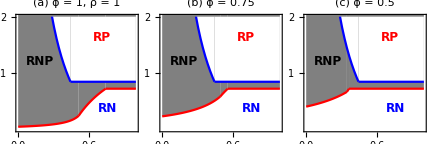
-Graphics-Defense CostIGP Strenght

```mathematica
Figure6abc = Panel[GraphicsRow[{Fig6a,Fig6b,Fig6c}, ImageSize-> 432, Spacings->0], {"Defense Cost",Rotate["IGP Strenght",Pi/2]},{Bottom,Left},Background->White]
```